Advent of Code 2019

### Problem 1

Part (a) asks us to apply a simple function to a list of integers.

```mathematica
t=Flatten@Import["~/Downloads/Advent2019/input1a.txt","CSV"];
Fold[#1+Floor[#2/3]-2&,0,t]
```

3210097

Part (b) asks us to apply a function repeatedly to each integer until it turns negative.

```mathematica
f[n_]:=Total@Most@Rest@NestWhileList[Floor[#/3]-2&,n,#>0&]
Total@Map[f,t]
```

4812287

I was curious about the nested function, so with some quick calculations I found an approximation that shows the asymptotic character of the function to be linear with coefficient 1/2.

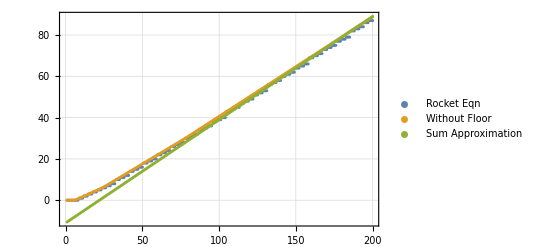

```mathematica
m=200;
g[n_]:=Total@Most@Rest@NestWhileList[#/3-2&,n,#>0&]
ListPlot[{Array[f,m],Array[g,m],Table[x/2-11,{x,m}]},PlotLegends->{"Rocket Eqn","Without Floor","Sum Approximation"}]
```

### Problem 2

Part (a) requires us to transform the string in a manner similar to a Turing machine.

```mathematica
problemInput=Flatten@Import["~/Downloads/Advent2019/input2a.txt","CSV"];
f[noun_,verb_,input_]:=Module[{i,t},
(* Set the inputs *)
t=input;t[[2]]=noun;t[[3]]=verb;
(* Set up the op codes *)
ops={1->Plus,2->Times};
(* Grab 4 values at a time and proceed through until 99 *)
For[i=1,i<Length[t]-3,i=i+4,
{op,i1,i2,o}=t[[i;;i+3]];
If[op==99,Break[],
t[[o+1]]=t[[i1+1]]~(op/.ops)~t[[i2+1]]];];
t[[1]]]
f[12,2,problemInput]
```

6087827

Test inputs.

```mathematica
t={1,0,0,0,99};
f[0,0,t]
t={2,3,0,3,99};
f[3,0,t]
t={2,4,4,5,99,0};
f[4,4,t]
t={1,1,1,4,99,5,6,0,99};
f[1,1,t]
```

2

2

2

30

Part (b) requires us to find the inputs that cause the program to generate the output 19690720. The inputs are the two values I switched in the beginning of the input. I ran into an issue with the function above using the same variable as the Table function below. I had to specify that the index variable in the Module block above is local, which fixed the issue.

```mathematica
{noun,verb,_}=First@Select[Flatten[Table[{i,j,f[i,j,problemInput]},{i,0,99},{j,0,99}],1],#[[3]]==19690720&];
100*noun+verb
```

5379

### Problem 3

Part (a) asks us to find the closest intersection point (in Manhattan distance) of two random walks starting from the origin, specified in a format very similar to turtle graphics.

```mathematica
{t1,t2}=StringSplit[#,","]&/@StringSplit[Import["~/Downloads/Advent2019/input3a.txt"],"\n"];
f[entry_]:={First[#],FromDigits@ToExpression@Rest[#]}&@Characters@entry
directions={"R"->{1,0},"L"->{-1,0},"U"->{0,1},"D"->{0,-1}};
line[start_,dir_,steps_]:=Rest@NestList[#+(dir/.directions)&,start,steps]
rw1=Fold[#1~Join~line[#1[[-1]],#2[[1]],#2[[2]]]&,{{0,0}},f/@t1];
rw2=Fold[#1~Join~line[#1[[-1]],#2[[1]],#2[[2]]]&,{{0,0}},f/@t2];
Min@Map[ManhattanDistance[{0,0},#]&,Complement[Intersection[rw1,rw2],{{0,0}}]]
```

1064

Part (b) is similar to part (a), except the distance function is now the sum of the path lengths to the intersection in both walks.

```mathematica
{t1,t2}=StringSplit[#,","]&/@StringSplit[Import["~/Downloads/Advent2019/input3a.txt"],"\n"];
f[entry_]:={First[#],FromDigits@ToExpression@Rest[#]}&@Characters@entry
directions={"R"->{1,0},"L"->{-1,0},"U"->{0,1},"D"->{0,-1}};
line[start_,dir_,steps_]:=Rest@NestList[#+(dir/.directions)&,start,steps]
rw1=Fold[#1~Join~line[#1[[-1]],#2[[1]],#2[[2]]]&,{{0,0}},f/@t1];
rw2=Fold[#1~Join~line[#1[[-1]],#2[[1]],#2[[2]]]&,{{0,0}},f/@t2];
wireDistance[wire_,point_]:=First@FirstPosition[wire,point]
distance[point_]:=wireDistance[rw1,point]+wireDistance[rw2,point]-2
Min@Map[distance,Complement[Intersection[rw1,rw2],{{0,0}}]]
```

25676

Test case.

```mathematica
rw1={{0,0},{0,1},{0,2},{1,2},{2,2},{1,2}};
rw2={{0,0},{1,0},{2,0},{3,0},{4,0},{3,0},{3,1},{3,2},{2,2},{1,2}};
wireDistance[rw1,{1,2}]
wireDistance[rw2,{1,2}]
```

4

10

### Problem 4

Part (a) asks us to count all the digits with non-decreasing digits and at least two identical consecutive digits.

```mathematica
a=273025;b=767253;t=Table[i,{i,a,b}];
f[n_]:=AnyTrue[Length/@(Gather@IntegerDigits[n]),#≥2&]
Length@Select[t,f[#]&&Sort@IntegerDigits[#]==IntegerDigits[#]&]
```

910

Part (b) asks for the same digits, except that the identical consecutive digits cannot be part of a larger group of consecutive digits. That is, the number has to contain at least one run of exactly two identical digits.

```mathematica
a=273025;b=767253;t=Table[i,{i,a,b}];
f[n_]:=AnyTrue[Length/@(Gather@IntegerDigits[n]),#==2&]
Length@Select[t,f[#]&&Sort@IntegerDigits[#]==IntegerDigits[#]&]
```

598

### Problem 5